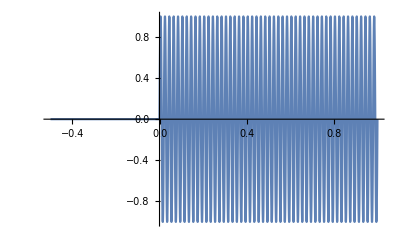

```mathematica
fc=50;fe=1;bw=20;timeSeries[t_]=Sin[2π fc t]HeavisidePi[fe t-1/2];
Plot[timeSeries[t],{t,-.5,1},PlotPoints->200,Filling->Axis]
```

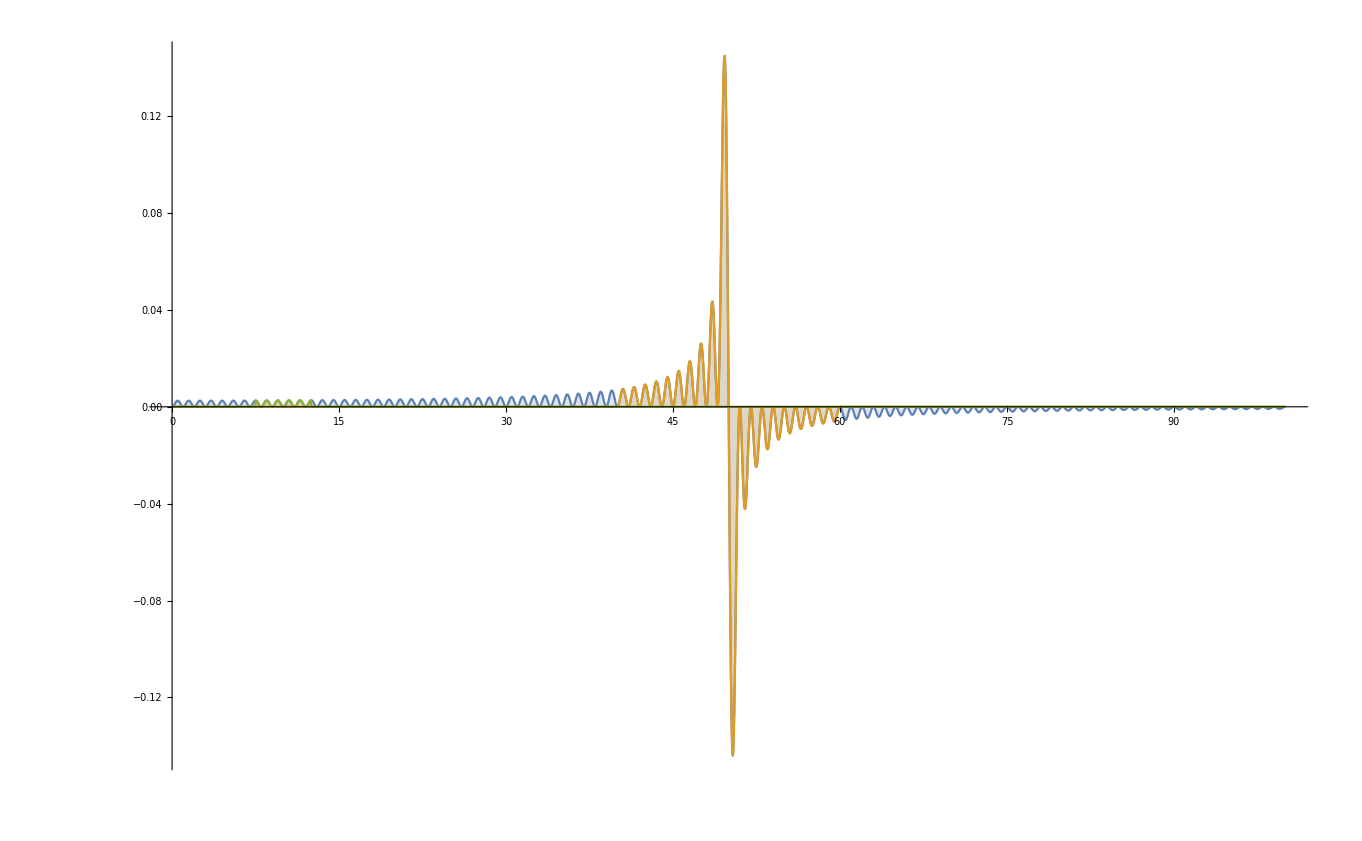

```mathematica
ft[ω_]=FullSimplify[FourierTransform[timeSeries[t],t,ω],Assumptions->{fc>0,fe>0,fc>fe}];
filter[ω_]=HeavisidePi[(ω/(2π)-fc)/bw];
Plot[{Re[ft[2π f]],Re[ft[2π f]*filter[2π f]],Re[ft2[2π f]]},{f,0,2 fc},PlotRange->All,Filling->Axis]
ft2[ω_]=ft[ω]*filter[ω];
```

```mathematica
FullSimplify[ComplexExpand[Re[ft[ω]*filter[ω]]]]
```

(50 √(2 π) (-1+Cos[ω]) (HeavisideTheta[-25 π+ω]-HeavisideTheta[-15 π+ω]))/(10000 π^2-ω^2)

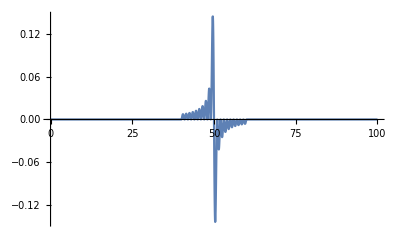

```mathematica
Plot[FullSimplify[ComplexExpand[Re[ft[2π f]*filter[2π f]]]],{f,0,100}]
```

```mathematica
FullSimplify[Re[ft2[2π f]]]
```

(25 Re[((-1+ⅇ^(2 ⅈ f π)) HeavisidePi[2-f/5])/(-2500+f^2)])/(√2 π^(3/2))

```mathematica
ift[t_]=InverseFourierTransform[(50 √(2 π) (-1+Cos[ω]) (HeavisideTheta[-25 π+ω]-HeavisideTheta[-15 π+ω]))/(10000 π^2-ω^2),ω,t]
```

$Aborted

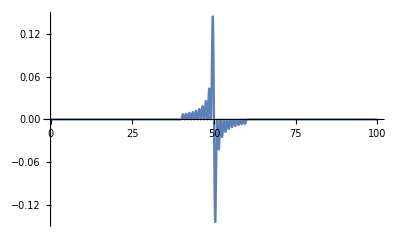

```mathematica
Plot[{Re[ft[2π f]*filter[2π f]]},{f,0,2 fc},PlotRange->All,Filling->Axis]
```

```mathematica
Re[ft[2π f]*filter[2π f]]
```

-50 √(2 π) Re[((-1+ⅇ^(2 ⅈ f π)) HeavisidePi[1/20 (-50+f)])/(10000 π^2-4 f^2 π^2)]

```mathematica
Re[ft2[2π f]]
```

-50 √(2 π) Re[((-1+ⅇ^(2 ⅈ f π)) HeavisidePi[1/5 (-10+f)])/(10000 π^2-4 f^2 π^2)]

```mathematica
Re[ft2[2π f]]
```

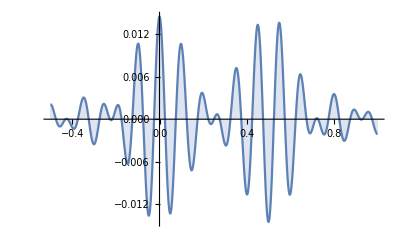

```mathematica
Plot[Re[ift[t]],{t,-.5,1},PlotPoints->200,Filling->Axis]
```

```mathematica
(ⅇ^(-20 ⅈ π t) (-CosIntegral[-5 π t]+CosIntegral[5 π t]+ExpIntegralEi[5/2 ⅈ π (1-2 t)]-ExpIntegralEi[5/2 ⅈ π (-1+2 t)]+2 ⅈ SinIntegral[5 π t]+ⅇ^(40 ⅈ π t) (-CosIntegral[35 π t]+CosIntegral[45 π t]+ExpIntegralEi[35/2 ⅈ π (1-2 t)]-ExpIntegralEi[45/2 ⅈ π (1-2 t)]+ⅈ SinIntegral[35 π t]-ⅈ SinIntegral[45 π t])))/(4 π)/.t->1//N
```

-0.00257443-0.487446 ⅈ

```mathematica
Needs["FourierSeries`"]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

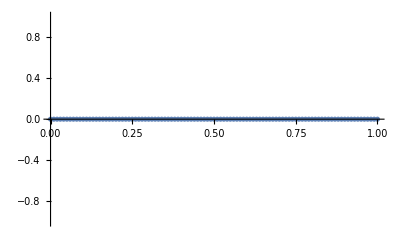

```mathematica
ListPlot[{#,Re[NIntegrate[1/(√(2π))(50 √(2 π) (-1+Cos[ω]) (HeavisideTheta[-25 π+ω]-HeavisideTheta[-15 π+ω]))/(10000 π^2-ω^2),{ω,-∞,∞}]]}&/@Range[0,1,.01]]
```

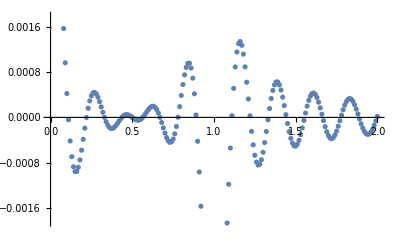

```mathematica
ListPlot[{#,Re[NIntegrate[1/(√(2π))ft[ω]Exp[-ⅈ ω #],{ω,0,600}]]}&/@Range[0,2,.01]]
```

```mathematica
Plot[timeSeries[t],{t,-.5,1},PlotPoints->200,Filling->Axis]
```

-Graphics-

```mathematica
Integrate[1/(√(2π))timeSeries[t]Exp[ⅈ ω t],{t,-∞,∞}]
```

-(50 (-1+ⅇ^(ⅈ ω)) √(2 π))/(10000 π^2-ω^2)

```mathematica
ft[ω]
```

-(50 (-1+ⅇ^(ⅈ ω)) √(2 π))/(10000 π^2-ω^2)

```mathematica
InverseFourierTransform[-(50 (-1+ⅇ^(ⅈ ω)) √(2 π))/(10000 π^2-ω^2),ω,t]
```

$Aborted

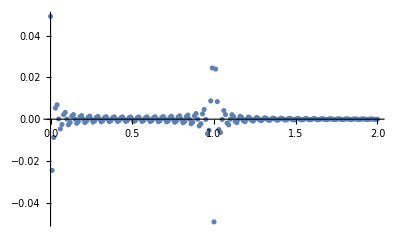

```mathematica
ListPlot[ParallelTable[{t,Re[Chop[NIntegrate[1/(√(2π))(-(50 (-1+ⅇ^(ⅈ ω)) √(2 π))/(10000 π^2-ω^2)Exp[-ⅈ ω t]),{ω,2π 20,2π 80}]]]},{t,0,2,.01}],PlotRange->All]
```

```mathematica
timeSeries[t]
```

HeavisidePi[1/2-t] Sin[100 π t]